# FormCalc: top-quark pair production (parton level)

```mathematica
Exit[];
```

### Set Up

```mathematica
$Language="English";
<<FeynArts`
<<FormCalc`
```

FeynArts 3.11 (3 Aug 2020)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.9 (28 Aug 2020)

by Thomas Hahn

### Topology

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebf/cedf/ef.m, 0 diagrams

> Top. 3 aebf/cfde/ef.m, 0 diagrams

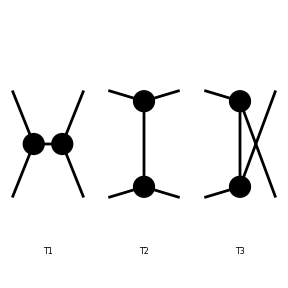

FeynArtsGraphics[2→2][([T1] | [T2] | [T3]
Null | Null | Null
Null | Null | Null)]

```mathematica
topologies=CreateTopologies[0,2->2, ExcludeTopologies-> Irreducible];
Paint[topologies]
```

### Diagram

```mathematica
InitializeModel["dim_6_c6_c8c", GenericModel -> "dim_6_c6_c8c"];
```

loading generic model file /Users/jaco/Documents/PhD/CAPP21/Thomas Hahn Lecture 4/FormCalc/FeynArts-3.11/Models/dim_6_c6_c8c.gen

> $GenericMixing is OFF

generic model {dim_6_c6_c8c} initialized

loading classes model file /Users/jaco/Documents/PhD/CAPP21/Thomas Hahn Lecture 4/FormCalc/FeynArts-3.11/Models/dim_6_c6_c8c.mod

> 49 particles (incl. antiparticles) in 22 classes

> $CounterTerms are ON

> 124 vertices

classes model {dim_6_c6_c8c} initialized

Excluding 0 Generic, 3 Classes, and 3 Particles fields

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

> Top. 2: 0 Classes insertions

> Top. 3: 0 Classes insertions

Restoring 0 Generic, 3 Classes, and 3 Particles fields

in total: 1 Classes insertion

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

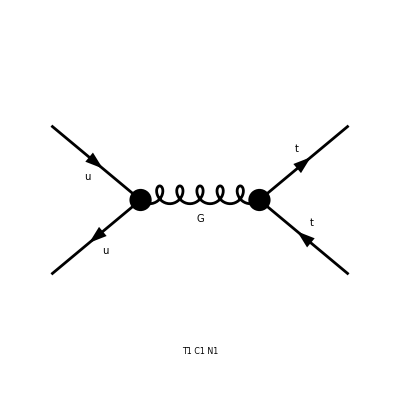

```mathematica
diagrams=InsertFields[topologies,
{F[3, {1}], -F[3, {1}]}->{F[30], -F[30]},InsertionLevel->{Classes},
Model->"dim_6_c6_c8c", GenericModel-> "dim_6_c6_c8c", ExcludeParticles-> {V[1],V[2],S[1]}
];

Paint[diagrams];
```

### Amplitude

```mathematica
ClearProcess[];
amplitude=CalcFeynAmp[CreateFeynAmp[diagrams], FermionChains->VA];
squared=SquaredME[amplitude];
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/jaco/fc-amp-1.frm

running FORM...

ok

### Helicities

```mathematica
(*Only for fermions*)
_Hel=0;
squared=squared//.HelicityME[amplitude];
```

> 81 helicity matrix elements

preparing FORM code in /Users/jaco/fc-hel-5.frm

running FORM...

ok

### Colour

```mathematica
squared = ExpandSums[squared//.ColourME[amplitude]];
```

### Polarizations

```mathematica
rawResult = PolarizationSum[squared,GaugeTerms->False]//.Join[Subexpr[],Abbr[]];
result=4/(3 * 3)*rawResult; (*Multiply by two for each ougoing fermion, divide by the colour factor (8 for gluons, 3 for quarks) and by initial vector particles*)
```

preparing FORM code in /Users/jaco/fc-pol-13.frm

running FORM...

ok

### Replacements

```mathematica
repl = {vevhat-> v, LambdaSMEFT-> Λ, MU-> 0, MU2-> 0, MD-> 0, MD2-> 0};
```

```mathematica
MyResult = result//.Join[Abbr[],Subexpr[], M$FACouplings,{Den[p2_,m2_]:>1/(p2-m2)},repl ];
```

```mathematica
MyResultSimplified=Simplify[MyResult, Assumptions->{Element[Λ , Reals], Element[v, Reals], Element[ctGRe, Reals], Element[cuGRe, Reals], Element[cuGIm, Reals], Element[ctGIm, Reals]}]
```

1/(9 Alfas2 GS π S^2 Λ^8)8 Alfas (2 Alfas2 GS π^2 (2 MT2^2+T^2+2 MT2 (S-T-U)+U^2) Λ^4 (-2 √2 ctGRe MT v+GS Λ^2)^2+2 √2 Alfas2 ctGRe GS π^2 v Λ^4 (-2 √2 ctGRe (S U (S+U)-2 MT2 U (2 S+T+U)+MT2^2 (S+4 U)) v+4 GS MT (MT2^2-T U) Λ^2)+2 √2 Alfas2 GS π^2 v Λ^4 (√2 ctGIm^2 (-2 S U (S+U)+4 MT2 U (2 S+T+U)-2 MT2^2 (S+4 U)) v-4 ctGRe MT (MT2^2-T U) (2 √2 ctGRe MT v-GS Λ^2))+(Alfas (cuGIm^2+cuGRe^2) π S (T-U)^2 v^3 (ctGIm^2 GS S v+ctGRe (ctGRe GS S v-4 √2 Alfas MT π Λ^2))+GS v (ctGRe GS MT v-√2 Alfas π Λ^2) (cuGRe^2 S v (ctGRe GS MT (T-U)^2 v-4 (MT2-U) (MT2-S-U) (ctGRe GS MT v-√2 Alfas π Λ^2))+cuGIm^2 v (ctGRe GS MT S (T-U)^2 v+2 (2 MT2 S (S+2 U)-2 S (MT2^2+U (S+U))) (ctGRe GS MT v-√2 Alfas π Λ^2)))) (yutop[1,1]Superscript[*]) yutop[1,1])

```mathematica
dim6Sq = Collect[MyResultSimplified//Expand, 1/Λ^2];
dim6Sm = dim6Sq/.{Λ^b_/;b≠0->0};
dim6Quad = (dim6Sq - dim6Sm)/.{Λ^b_/;b≠-4->0} ;
dim6Lin =(dim6Sq -  dim6Sm)/.{Λ^b_/;b≠-2->0} ;
```

```mathematica
dim6Sm = dim6Sm//.{GS -> √(4π Alfas)}//FullSimplify
```

(64 Alfas2 π^2 (2 MT2^2+T^2+2 MT2 (S-T-U)+U^2))/(9 S^2)

```mathematica
dim6Lin = dim6Lin//.{GS -> √(4π Alfas)}//FullSimplify
```

-(128 √2 Alfas^(3/2) ctGRe MT π^(3/2) (2 MT2 (S-T-U)+(T+U)^2) v)/(9 S^2 Λ^2)

```mathematica
dim6Quad = dim6Quad//.{GS -> √(4π Alfas)}//FullSimplify
```

-1/(9 S^2 Λ^4)64 Alfas π v^2 (ctGIm^2 (S U (S+U)-2 MT2 U (2 S+T+U)+MT2^2 (S+4 U))+ctGRe^2 (S U (S+U)+MT2^2 (-3 S+4 T+8 U)-2 MT2 (T^2+3 T U+2 U (S+U)))-(cuGIm^2+cuGRe^2) S (MT2-U) (-MT2+S+U) Abs[yutop[1,1]]^2)

### Cross section

```mathematica
Clear[pf, pi]
```

```mathematica
pf = pf/.Solve[{√S== √(MT2 +pf^2) + √(MT2 +pf^2)}, pf][[2]]
```

1/2 √(-4 MT2+S)

```mathematica
pi = (pi/.Solve[S ==(√(pi^2)+√(pi^2))^2, pi])[[2]];
```

```mathematica
prefacdOmega = 1/(64 π^2 S)*pf/pi
```

(√(-4 MT2+S))/(64 π^2 S^(3/2))

```mathematica
integraldOmega=dim6Sm//.{T->MT2+MT2-S-U, U-> MT2-2pi*(√(MT2+pf^2)-pf Cos[θ])};
diffXSectiondtheta=2π * prefacdOmega*integraldOmega * Sin[θ]
```

1/(9 S^(7/2))2 Alfas2 π √(-4 MT2+S) (2 MT2^2+2 MT2 (-2 MT2+2 S)+(MT2-√S (√(MT2+1/4 (-4 MT2+S))-1/2 √(-4 MT2+S) Cos[θ]))^2+(MT2-S+√S (√(MT2+1/4 (-4 MT2+S))-1/2 √(-4 MT2+S) Cos[θ]))^2) Sin[θ]

```mathematica
sigma = Integrate[diffXSectiondtheta, {θ, 0, π}, Assumptions->{Element[S, Reals]}]
```

(8 Alfas2 π √(-4 MT2+S) (2 MT2+S))/(27 S^(5/2))

```mathematica
sigma/.{cuGIm-> 0, cuGRe-> 0 ,ctGIm-> 0}
```

(8 Alfas2 π √(-4 MT2+S) (2 MT2+S))/(27 S^(5/2))